# Two-Site Hubbard Model

```mathematica
Quit[]
```

```mathematica
<<Q3`Fock`
```

Q3/Cauchy.m v1.10 (2020-11-02) Mahn-Soo Choi

Q3/Grassmann.m v1.1 (2020-11-01) Mahn-Soo Choi

Q3/Pauli.m v1.3 (2020-11-02) Mahn-Soo Choi

Q3/Fock.m v1.9 (2020-11-02) Mahn-Soo Choi

Let us first declare fermion operators and control parameters:

```mathematica
Let[Fermion,c,d]
Let[Real,ϵ,t,U]
```

The single-particle part of the two isolated quantum dots is given by

```mathematica
H0=ϵ*Q[d[{1,2},All]]
```

ϵ (d_(1,↓)^†d_(1,↓)+d_(1,↑)^†d_(1,↑)+d_(2,↓)^†d_(2,↓)+d_(2,↑)^†d_(2,↑))

So, the hopping part is given by

```mathematica
Ht=-t*PlusDagger@FockHopping[{d[1,All],d[2,All]}]
```

-t (d_(1,↓)^†d_(2,↓)+d_(1,↑)^†d_(2,↑)+d_(2,↓)^†d_(1,↓)+d_(2,↑)^†d_(1,↑))

and the overall single-particle part is given by

```mathematica
H1=H0+Ht
```

-t (d_(1,↓)^†d_(2,↓)+d_(1,↑)^†d_(2,↑)+d_(2,↓)^†d_(1,↓)+d_(2,↑)^†d_(1,↑))+ϵ (d_(1,↓)^†d_(1,↓)+d_(1,↑)^†d_(1,↑)+d_(2,↓)^†d_(2,↓)+d_(2,↑)^†d_(2,↑))

### On-site interactions

```mathematica
H2=U(Q[d[1,Up]]**Q[d[1,Down]]+Q[d[2,Up]]**Q[d[2,Down]])
```

U (d_(1,↓)^†d_(1,↑)^†d_(1,↑)d_(1,↓)+d_(2,↓)^†d_(2,↑)^†d_(2,↑)d_(2,↓))

The total Hamiltonian for the DQD is given by

```mathematica
HH=H1+H2
```

-t (d_(1,↓)^†d_(2,↓)+d_(1,↑)^†d_(2,↑)+d_(2,↓)^†d_(1,↓)+d_(2,↑)^†d_(1,↑))+ϵ (d_(1,↓)^†d_(1,↓)+d_(1,↑)^†d_(1,↑)+d_(2,↓)^†d_(2,↓)+d_(2,↑)^†d_(2,↑))+U (d_(1,↓)^†d_(1,↑)^†d_(1,↑)d_(1,↓)+d_(2,↓)^†d_(2,↑)^†d_(2,↑)d_(2,↓))

Take a look at the connectivity of the model.

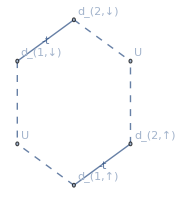

```mathematica
GraphForm[HH,ImageSize->Small]
```

Here black thin lines indicate the hopping and the dashed lines represent the interaction.

### Many-body eigenstates

What about the N=2 states?

```mathematica
basis2={Dagger@d[1,Up]**Dagger@d[1,Down],Dagger@d[2,Up]**Dagger@d[2,Down],Dagger@d[1,Up]**Dagger@d[2,Up],Dagger@d[1,Up]**Dagger@d[2,Down],
Dagger@d[1,Down]**Dagger@d[2,Up],Dagger@d[1,Down]**Dagger@d[2,Down]}**VacuumState
```

{-d_(1,↓)^†d_(1,↑)^†␣,-d_(2,↓)^†d_(2,↑)^†␣,d_(1,↑)^†d_(2,↑)^†␣,d_(1,↑)^†d_(2,↓)^†␣,d_(1,↓)^†d_(2,↑)^†␣,d_(1,↓)^†d_(2,↓)^†␣}

```mathematica
matH=Outer[Multiply,Dagger@basis2,HH**basis2];
matH//MatrixForm
```

(U+2 ϵ | 0 | 0 | -t | t | 0
0 | U+2 ϵ | 0 | -t | t | 0
0 | 0 | 2 ϵ | 0 | 0 | 0
-t | -t | 0 | 2 ϵ | 0 | 0
t | t | 0 | 0 | 2 ϵ | 0
0 | 0 | 0 | 0 | 0 | 2 ϵ)

```mathematica
spectrum[U_,ϵ_,t_]=matH
```

{{U+2 ϵ,0,0,-t,t,0},{0,U+2 ϵ,0,-t,t,0},{0,0,2 ϵ,0,0,0},{-t,-t,0,2 ϵ,0,0},{t,t,0,0,2 ϵ,0},{0,0,0,0,0,2 ϵ}}